```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

FR$ClassesTranslation

## Top - G - G vertex

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

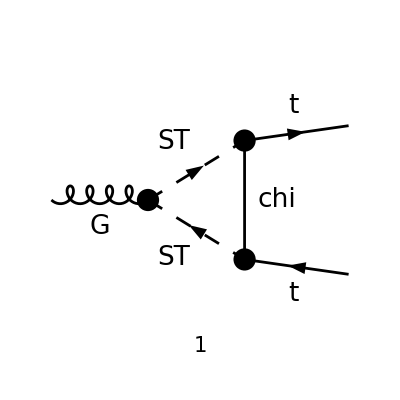

```mathematica
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]];
```

in total: 1 Particles amplitude

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-2 ⅈ π^2 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+ⅈ π^2 GS yDM^2 p2^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))-ⅈ π^2 GS yDM^2 p1^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))

```mathematica
ampEsimp=ampE//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1}
```

-2 ⅈ π^2 C00 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ π^2 GS yDM^2 p1^μ T_Col2Col3^Glu1 ((C1+2 C11) (γ·p1).(γ̄)^6-(C1+2 C12) (γ·p2).(γ̄)^6)+ⅈ π^2 GS yDM^2 p2^μ T_Col2Col3^Glu1 ((C1+2 C12) (γ·p1).(γ̄)^6-(C1+2 C11) (γ·p2).(γ̄)^6)

```mathematica
Expand[Collect[ampEsimp,{C00,C11,C12,C1},foo]]/.foo->FullSimplify
```

-2 ⅈ π^2 C00 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ π^2 C1 GS yDM^2 (p1^μ-p2^μ) T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6)-2 ⅈ π^2 C11 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6)+2 ⅈ π^2 C12 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)

### Default Values (High Mass Limit)

```mathematica
ampEeft=Limit[PaXEvaluate[ampE,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{s,0,0},{MT,0,0}}],mChi->mST]//Simplify;
Collect[ampEeft,{Epsilon,mST},Simplify]
```

(ⅈ GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(192 π^2 mST^2)+(ⅈ GS yDM^2 γ^μ.(γ̄)^6 (ℽ-log((4 π μ^2)/mST^2)) T_Col2Col3^Glu1)/(32 π^2)-(ⅈ GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(32 π^2 ε)

```mathematica
C00def=Limit[PaXEvaluate[PaVe[0,0,{0,0,0},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],mChi->mST]//Simplify
C1def=Limit[PaXEvaluate[PaVe[1,{0,0,0},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],mChi->mST]//Simplify
C11def=Limit[PaXEvaluate[PaVe[1,1,{0,0,0},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],mChi->mST]//Simplify
C12def=Limit[PaXEvaluate[PaVe[1,2,{0,0,0},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],mChi->mST]//Simplify
```

(ε (log(4 π)-ℽ)+ε log(μ^2/mST^2)+1)/(64 π^4 ε)

1/(96 π^4 mST^2)

-1/(192 π^4 mST^2)

-1/(384 π^4 mST^2)

### Decomposition in terms of Basic Scalar Integrals

```mathematica
C00eq =ChangeDimension[PaVeReduce[PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]],4]/.{D->4}//Simplify;
C1eq =ChangeDimension[PaVeReduce[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]],4]/.{D->4}//Simplify
C11eq =ChangeDimension[PaVeReduce[PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]],4]/.{D->4}//Simplify
C12eq =ChangeDimension[PaVeReduce[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]],4]/.{D->4}//Simplify
C00Effeq=(C00eq- 2 MT^2 (C1eq + C11eq + C12eq)- (s/2)(C1eq+2C12eq))//FullSimplify
```

(B_0(MT^2,mChi^2,mST^2)-B_0(s,mST^2,mST^2)-(mChi^2-mST^2+MT^2) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2))/(4 MT^2-s)

1/(4 MT^2 s (s-4 MT^2)^2)(-2 MT^2 (-2 mChi^2 (2 MT^2+s)+2 mST^2 (2 MT^2+s)-8 MT^2 s+4 MT^4+s^2) B_0(s,mST^2,mST^2)+2 (-8 MT^2 s+4 MT^4+s^2) (mChi^2-mST^2+MT^2) B_0(MT^2,mChi^2,mST^2)+4 MT^2 (-2 mChi^2 (mST^2 (2 MT^2+s)+2 MT^2 (MT^2-s))+mChi^4 (2 MT^2+s)+(mST^2-MT^2)^2 (2 MT^2+s)) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2)-2 (2 MT^2-s) (4 MT^2-s) A_0(mChi^2)+2 (2 MT^2-s) (4 MT^2-s) A_0(mST^2))

-1/(s (s-4 MT^2)^2)((2 MT^2+s) (mChi^2-mST^2+MT^2) B_0(MT^2,mChi^2,mST^2)+(2 mChi^2 (MT^2-s)-2 mST^2 (MT^2-s)-MT^2 (2 MT^2+s)) B_0(s,mST^2,mST^2)+(-mChi^2 (4 mST^2 (MT^2-s)-2 MT^2 s+4 MT^4+s^2)+2 mChi^4 (MT^2-s)+2 (mST^2-MT^2)^2 (MT^2-s)) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2)-(4 MT^2-s) A_0(mChi^2)+(4 MT^2-s) A_0(mST^2))

1/(4 (s-4 MT^2)^2)(2 s^2 B_0(MT^2,mChi^2,mST^2)-2 MT^2 s B_0(MT^2,mChi^2,mST^2)-24 mChi^2 MT^2 B_0(s,mST^2,mST^2)-2 mChi^2 s B_0(MT^2,mChi^2,mST^2)+2 mST^2 s B_0(MT^2,mChi^2,mST^2)+24 MT^4 B_0(MT^2,mChi^2,mST^2)+56 mChi^2 MT^2 B_0(MT^2,mChi^2,mST^2)-56 mST^2 MT^2 B_0(MT^2,mChi^2,mST^2)-6 mChi^2 s B_0(s,mST^2,mST^2)-8 MT^4 B_0(s,mST^2,mST^2)+24 mST^2 MT^2 B_0(s,mST^2,mST^2)-6 MT^2 s B_0(s,mST^2,mST^2)-s^2 B_0(s,mST^2,mST^2)+6 mST^2 s B_0(s,mST^2,mST^2)+2 (4 MT^2+s) (2 mChi^2 (3 mST^2+MT^2-s)-3 mChi^4-(mST-MT) (mST+MT) (3 mST^2+MT^2-s)) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2)+8 (s-4 MT^2) A_0(mChi^2)+32 MT^2 A_0(mST^2)-8 s A_0(mST^2))

```mathematica
ChangeDimension[PaVeReduce[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]],4]/.{D->4}//Simplify
```

(B_0(MT^2,mChi^2,mST^2)-B_0(s,mST^2,mST^2)-(mChi^2-mST^2+MT^2) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2))/(4 MT^2-s)

#### Simplifications to FortranForm

```mathematica
SetOptions[$Output,PageWidth->1000];
```

```mathematica
FortranForm[Collect[C00Effeq//.{PaVe[0,{s},{mST^2,mST^2}]->B0a,PaVe[0,{MT^2},{mChi^2,mST^2}]->B0b,
PaVe[0,{MT^2,MT^2,s},{mST^2,mChi^2,mST^2}]->C0a,PaVe[0,{},{mChi^2}]->A0a,PaVe[0,{},{mST^2}]->A0b,MT^2->mt2,MT^4->mt2^2,mChi^2->mchi2,mST^2->mst2},{A0a,A0b,B0a,B0b,C0a},FullSimplify]]
```

(2*A0a)/(-4*mt2 + s) - (2*A0b)/(-4*mt2 + s) + (C0a*(-3*mChi**4 + (2*mchi2 - mST**2 + MT**2)*(3*mst2 + mt2 - s))*(4*mt2 + s))/(2.*(-4*mt2 + s)**2) - (B0a*(6*mchi2 - 6*mst2 + 2*mt2 + s)*(4*mt2 + s))/(4.*(-4*mt2 + s)**2) + (B0b*(4*mt2*(7*mchi2 - 7*mst2 + 3*mt2) - (mchi2 - mst2 + mt2)*s + s**2))/(2.*(-4*mt2 + s)**2)

```mathematica
FortranForm[C1eq//.{PaVe[0,{s},{mST^2,mST^2}]->B0a,PaVe[0,{MT^2},{mChi^2,mST^2}]->B0b,
PaVe[0,{MT^2,MT^2,s},{mST^2,mChi^2,mST^2}]->C0a,MT^2->mt2,MT^4->mt2^2,mChi^2->mchi2,mST^2->mst2}]
```

(-B0a + B0b - C0a*(mchi2 - mst2 + mt2))/(4*mt2 - s)

```mathematica
FortranForm[C11eq//.{PaVe[0,{s},{mST^2,mST^2}]->B0a,PaVe[0,{MT^2},{mChi^2,mST^2}]->B0b,
PaVe[0,{MT^2,MT^2,s},{mST^2,mChi^2,mST^2}]->C0a,
PaVe[0,{},{mChi^2}]->A0a,PaVe[0,{},{mST^2}]->A0b,MT^2->mt2,MT^4->mt2^2,mChi^2->mchi2,mST^2->mst2}]
```

(-2*A0a*(2*mt2 - s)*(4*mt2 - s) + 2*A0b*(2*mt2 - s)*(4*mt2 - s) + 2*B0b*(mchi2 - mst2 + mt2)*(4*mt2**2 - 8*mt2*s + s**2) - 2*B0a*mt2*(4*mt2**2 - 8*mt2*s + s**2 - 2*mchi2*(2*mt2 + s) + 2*mst2*(2*mt2 + s)) + 4*C0a*mt2*(mChi**4*(2*mt2 + s) + (mst2 - mt2)**2*(2*mt2 + s) - 2*mchi2*(2*mt2*(mt2 - s) + mst2*(2*mt2 + s))))/(4.*MT**2*s*(-4*mt2 + s)**2)

```mathematica
FortranForm[C12eq//.{PaVe[0,{s},{mST^2,mST^2}]->B0a,PaVe[0,{MT^2},{mChi^2,mST^2}]->B0b,
PaVe[0,{MT^2,MT^2,s},{mST^2,mChi^2,mST^2}]->C0a,
PaVe[0,{},{mChi^2}]->A0a,PaVe[0,{},{mST^2}]->A0b,MT^2->mt2,MT^4->mt2^2,mChi^2->mchi2,mST^2->mst2}]
```

-((-(A0a*(4*mt2 - s)) + A0b*(4*mt2 - s) + B0b*(mchi2 - mst2 + mt2)*(2*mt2 + s) + B0a*(2*mchi2*(mt2 - s) - 2*mst2*(mt2 - s) - mt2*(2*mt2 + s)) + C0a*(2*mChi**4*(mt2 - s) + 2*(mst2 - mt2)**2*(mt2 - s) - mchi2*(4*mt2**2 + 4*mst2*(mt2 - s) - 2*mt2*s + s**2)))/(s*(-4*mt2 + s)**2))